## SHARE - Kinetic Monte Carlo

There is a more detailed description on Wikipedia

There are two types of Kinetic Monte Carlo, both deal with a state with many possible transitions and work by randomly selecting an atom to move.

Rejection

Randomly select which of all possible moves weighted by their respective absolute frequencies

Also known as

residence-time algorithm

n-fold way

Bortz-Kalos-Lebowitz (BKL) algorithm

Pro: more “simulated real time” per iteration

Con: more computation time per iteration

Rejection-free

Uniformly select a state and reject the move with a probability related to the relative frequency

Con: less “simulated real time” per iteration

Pro: less computation time per iteration

We use rejection-KMC

select random atom

find all possible transitions

randomly choose one of the possible transitions

accept transition with probability

P = 1-r/r_0

r is natural rate of selected transition

r_0 is maximum possible natural rate of any transition

## SHARE - French Group’s Model

solid is made of many columns of atoms

only atoms on the top of a stack can move

energy of an atom is (n J + J_0)

n is number of in-plane neighbors

J is in-plane bond strength

J_0 is bond strength to column

if atom is on substrate j_0→J_0-E_S (bond with substrate is weaker)

atom moves to any adjacent column with equal frequency

ν = e ^ - ( energy / k T)

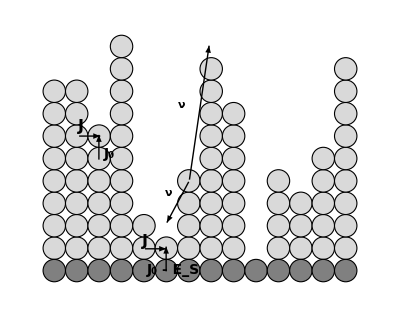

## SHARE - Our model

solid is real lattice, we use FCC

any atom with empty neighbor site can move

energy of an atom is (n_F+0.5 n_S) E_o

n_F is number of nearest neighbors in film

n_S is number of neighbors in substrate

E_o is bond energy with nearest neighbor in film

-Graphics3D-

What we ignore for now
At this point we assume an atom jumps with equal frequency into any spot with a given number of neighbors.

However, these frequency should also take into account the “bottleneck / throat / activation energy” required to pass through different.

Assuming the number of neighbors before and after are the same, there is still a difference depending on the number black atoms that make create an energetic mountain that must be crossed to make the move. Not only must the atom break all bonds, it must also go through this highly unstable state when it is half-way through jump.

-Graphics3D-

## Development

### indexToCoordinate

#### definitions

```mathematica
indexToCoordinate[{x_,y_,z_,1},"FCC"]:={x,y,z}
indexToCoordinate[{x_,y_,z_,2},"FCC"]:={x,y,z}+{0.5,0.5,0.0}
indexToCoordinate[{x_,y_,z_,3},"FCC"]:={x,y,z}+{0.5,0.0,0.5}
indexToCoordinate[{x_,y_,z_,4},"FCC"]:={x,y,z}+{0.0,0.5,0.5}
```

#### examples

```mathematica
indexToCoordinate[{2,3,4,4},"FCC"]
```

{2.,3.5,4.5}

### createSolid

#### definition

```mathematica
createSolid[
	w_Integer,
	d_Integer,
	h_Integer,
	geometry_String
] := 
Block[
	{atomsPerLatticeSite, allAtoms},

	Set[
		atomsPerLatticeSite, 
		Switch[geometry,"FCC",4]
	];

	Set[
		allAtoms,
		Flatten[
			Table[
				{x,y,z,i},
				{x,1,w},
				{y,1,d},
				{z,1,h},
				{i,1,atomsPerLatticeSite}
			],
			3
		]
	];

	Set[
		solidSites,
		AssociationMap[
			indexToCoordinate[#,geometry]&,
			allAtoms
		]
	]

] /; 
Or[
	StringMatchQ[geometry, "FCC"],
	StringMatchQ[geometry, "FCC"]
]
```

#### example

```mathematica
createSolid[2,2,2,"FCC"]
ListPointPlot3D@solidSites
```

<|{1,1,1,1}→{1,1,1},{1,1,1,2}→{1.5,1.5,1.},{1,1,1,3}→{1.5,1.,1.5},{1,1,1,4}→{1.,1.5,1.5},{1,1,2,1}→{1,1,2},{1,1,2,2}→{1.5,1.5,2.},{1,1,2,3}→{1.5,1.,2.5},{1,1,2,4}→{1.,1.5,2.5},{1,2,1,1}→{1,2,1},{1,2,1,2}→{1.5,2.5,1.},{1,2,1,3}→{1.5,2.,1.5},{1,2,1,4}→{1.,2.5,1.5},{1,2,2,1}→{1,2,2},{1,2,2,2}→{1.5,2.5,2.},{1,2,2,3}→{1.5,2.,2.5},{1,2,2,4}→{1.,2.5,2.5},{2,1,1,1}→{2,1,1},{2,1,1,2}→{2.5,1.5,1.},{2,1,1,3}→{2.5,1.,1.5},{2,1,1,4}→{2.,1.5,1.5},{2,1,2,1}→{2,1,2},{2,1,2,2}→{2.5,1.5,2.},{2,1,2,3}→{2.5,1.,2.5},{2,1,2,4}→{2.,1.5,2.5},{2,2,1,1}→{2,2,1},{2,2,1,2}→{2.5,2.5,1.},{2,2,1,3}→{2.5,2.,1.5},{2,2,1,4}→{2.,2.5,1.5},{2,2,2,1}→{2,2,2},{2,2,2,2}→{2.5,2.5,2.},{2,2,2,3}→{2.5,2.,2.5},{2,2,2,4}→{2.,2.5,2.5}|>

-Graphics3D-

### fillRegion

#### definition

```mathematica
fillRegion[desiredFinalRegion_]:=Module[
{containingCuboid,rmf},
containingCuboid=BoundingRegion[DiscretizeRegion@desiredFinalRegion,"MinCuboid"];
createSolid[
Ceiling@containingCuboid[[2,1]],
Ceiling@containingCuboid[[2,2]],
Ceiling@containingCuboid[[2,3]],
"FCC"
];
rmf=RegionMember[desiredFinalRegion];
solidSites=Select[solidSites,rmf];
]
```

#### SHARE - usage

name any region and have it filled with solid sites

```mathematica
testRegion=Ball[{10,10,10},4];
fillRegion[testRegion];
ListPointPlot3D[solidSites]
Show[{ListPointPlot3D[solidSites],Graphics3D@testRegion}]
```

-Graphics3D-

-Graphics3D-

It will drop points below x=1

```mathematica
testRegion=Ball[{0,0,0},4];
fillRegion[testRegion];
ListPointPlot3D[solidSites]
Show[{ListPointPlot3D[solidSites],Graphics3D@testRegion}]
```

-Graphics3D-

-Graphics3D-

do it with any MeshRegion

```mathematica
testRegion=MeshRegion[{{0,0,0},{10,0,0},{10,10,0},{0,10,0},{5,5,20}},{Tetrahedron[{1,2,3,5}],Tetrahedron[{1,3,4,5}]}];
fillRegion[testRegion];
ListPointPlot3D[solidSites]
Show[{ListPointPlot3D[solidSites],DiscretizeRegion@testRegion}]
```

-Graphics3D-

-Graphics3D-

### cutSolid

#### definition

```mathematica
cutSolid[region_]:=Block[
{rmf},
rmf=RegionMember[region];
solidSites=Select[solidSites,!rmf@#&]
]
```

#### example

```mathematica
createSolid[2,2,2,"FCC"];
Length@solidSites;
ListPointPlot3D[solidSites];
Show[{ListPointPlot3D[solidSites],Graphics3D@Cuboid[{0,0,0},{2,2,2}]}]
cutSolid[Cuboid[{0,0,0},{2,2,2}]];
Length@solidSites;
ListPointPlot3D[solidSites]
```

-Graphics3D-

-Graphics3D-

### neighbors

#### FCC

```mathematica
nbrC12 = Compile[{{x,_Integer},{y,_Integer},{z,_Integer}},
{
{x,y-1,z,2},
{x-1,y-1,z,2},
{x,y,z,2},
{x-1,y,z,2},

{x,y,z-1,3},
{x-1,y,z-1,3},
{x-1,y,z,3},
{x,y,z,3},

{x,y-1,z,4},
{x,y,z,4},
{x,y,z-1,4},
{x,y-1,z-1,4}
},
"RuntimeOptions"->"Speed"
];
```

```mathematica
nbrC11 = Compile[{{x,_Integer},{y,_Integer},{z,_Integer}},
{
{x,y-1,z,2},
{x-1,y-1,z,2},
{x,y,z,2},
{x-1,y,z,2},

{x-1,y,z,3},
{x,y,z,3},

{x,y-1,z,4},
{x,y,z,4}
},
"RuntimeOptions"->"Speed"
];
```

```mathematica
nbrC22 = Compile[{{x,_Integer},{y,_Integer},{z,_Integer}},
{
{x+1,y+1,z,1},
{x+1,y,z,1},
{x,y,z,1},
{x,y+1,z,1},

{x,y,z,4},
{x,y+1,z,3},
{x,y,z,3},
{x+1,y,z,4},

{x,y+1,z-1,3},
{x,y,z-1,4},
{x,y,z-1,3},
{x+1,y,z-1,4}
},
"RuntimeOptions"->"Speed"
];
```

```mathematica
nbrC21 = Compile[{{x,_Integer},{y,_Integer},{z,_Integer}},
{
{x+1,y+1,z,1},
{x+1,y,z,1},
{x,y,z,1},
{x,y+1,z,1},

{x,y,z,4},
{x,y+1,z,3},
{x,y,z,3},
{x+1,y,z,4}
},
"RuntimeOptions"->"Speed"
];
```

```mathematica
nbrC3 = Compile[{{x,_Integer},{y,_Integer},{z,_Integer}},
{
{x,y,z,1},
{x+1,y,z,1},
{x+1,y,z+1,1},
{x,y,z+1,1},

{x,y,z,2},
{x,y-1,z,2},
{x,y,z,4},
{x,y-1,z,4},

{x+1,y,z,4},
{x+1,y-1,z,4},
{x,y-1,z+1,2},
{x,y,z+1,2}
},
"RuntimeOptions"->"Speed"
];
```

```mathematica
nbrC4 = Compile[{{x,_Integer},{y,_Integer},{z,_Integer}},
{
{x,y,z,1},
{x,y+1,z,1},
{x,y+1,z+1,1},
{x,y,z+1,1},

{x-1,y,z,2},
{x-1,y,z,3},
{x-1,y+1,z,3},
{x-1,y,z+1,2},

{x,y,z+1,2},
{x,y+1,z,3},
{x,y,z,3},
{x,y,z,2}
},
"RuntimeOptions"->"Speed"
];
```

include substrate

```mathematica
neighbors[site:{x_,y_,z_,index_},"FCC"]:=
Switch[
index,
1,nbrC12[x,y,z],
2,nbrC22[x,y,z],
3,nbrC3[x,y,z],
4,nbrC4[x,y,z]
]
```

do not include substrate

```mathematica
neighbors2[site:{x_,y_,z_,index_},"FCC"]:=
Switch[
index,
1,If[
z==1,
nbrC11[x,y,z],
nbrC12[x,y,z]
],
2,If[
z==1,
nbrC21[x,y,z],
nbrC22[x,y,z]
],
3,nbrC3[x,y,z],
4,nbrC4[x,y,z]
]
```

#### example

```mathematica
Graphics3D[{
EdgeForm@Black,FaceForm@None,
Cuboid[#,#+{1,1,1}]&/@(Tuples[Range[0,2],3]),
FaceForm@Black,Opacity[.2],
Sphere[indexToCoordinate[{1,1,1,1},"FCC"],.25],
FaceForm@Red,Opacity[.2],
Sphere[indexToCoordinate[{1,1,1,2},"FCC"],.25],
FaceForm@Green,Opacity[1],
Sphere[#,.1]&/@(indexToCoordinate[#,"FCC"]&/@neighbors[{1,1,1,2},"FCC"])
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
EdgeForm@{Opacity[0.3],Black},FaceForm@None,
Cuboid[#,#+{1,1,1}]&/@(Tuples[Range[0,2],3]),
FaceForm@Black,Opacity[.4],
Sphere[indexToCoordinate[{1,1,1,2},"FCC"],.1],
FaceForm@Green,Opacity[1],
Sphere[#,.1]&/@(indexToCoordinate[#,"FCC"]&/@neighbors[{1,1,1,2},"FCC"]),
Arrow[{indexToCoordinate[{1,1,1,1},"FCC"],indexToCoordinate[{1,1,1,2},"FCC"]}],
Text[Style["E_0",FontWeight->Bold],{0,0,.15}+1/2(indexToCoordinate[{1,1,1,1},"FCC"]+indexToCoordinate[{1,1,1,2},"FCC"])]
}]
```

-Graphics3D-

### findSurface

#### definition

```mathematica
inBulkQ[site_,geometry_]:=And@@(
Or[KeyExistsQ[solidSites,#],#[[3]]<1]
&/@neighbors[site,geometry]
)
```

```mathematica
getSurface[geometry_]:=(surfaceSites=KeySelect[solidSites,!inBulkQ[#,geometry]&])
getBulk[geometry_]:=(bulkSites=KeySelect[solidSites,inBulkQ[#,geometry]&])
```

```mathematica
findSurface[geometry_]:=(
getSurface[geometry];
getBulk[geometry];
)
```

#### example

```mathematica
ass=AssociationMap[f,Range@21];
partition[ass,5]
```

partition[<|1→f[1],2→f[2],3→f[3],4→f[4],5→f[5],6→f[6],7→f[7],8→f[8],9→f[9],10→f[10],11→f[11],12→f[12],13→f[13],14→f[14],15→f[15],16→f[16],17→f[17],18→f[18],19→f[19],20→f[20],21→f[21]|>,5]

```mathematica
ass=AssociationMap[f,Range@21];
partition[ass,3]
```

partition[<|1→f[1],2→f[2],3→f[3],4→f[4],5→f[5],6→f[6],7→f[7],8→f[8],9→f[9],10→f[10],11→f[11],12→f[12],13→f[13],14→f[14],15→f[15],16→f[16],17→f[17],18→f[18],19→f[19],20→f[20],21→f[21]|>,3]

```mathematica
ass=AssociationMap[f,Range@8];
partition[ass,10]
```

partition[<|1→f[1],2→f[2],3→f[3],4→f[4],5→f[5],6→f[6],7→f[7],8→f[8]|>,10]

```mathematica
createSolid[2,2,2,"FCC"];
Length@solidSites
findSurface["FCC"]
Total[Query[All,Length@#&]@surfaceSites]
Total[Query[All,Length@#&]@bulkSites]
```

32

78

18

### siteOccupiedQ

#### definition

```mathematica
siteOccupiedQ[site_]:=Or[
KeyExistsQ[surfaceSites,site],
KeyExistsQ[bulkSites,site],
site[[3]]<1
]
```

#### usage

```mathematica
createSolid[2,2,2,"FCC"];
siteOccupiedQ[{1,1,1,1}]
siteOccupiedQ[{-1,-1,-1,1}]
```

True

True

### viewSolid

#### definition

```mathematica
Options[viewSolid]={"start" -> None, "end"->None, "highlight"->{}, "ImageSize"->Inherited};

viewSolid[surfaceSites_,bulkSites_,geometry_, OptionsPattern[]]:=Module[
{radius},
radius=Switch[geometry,
"FCC",.25
];
Graphics3D[{
Red,Sphere[#,radius]&/@Values@surfaceSites,
Green,Sphere[#,radius]&/@Values@bulkSites,
Black,Sphere[#,radius]&/@OptionValue["highlight"],
If[
OptionValue["start"]===None,
{},
{Blue,Sphere[OptionValue["start"],radius]}
],
If[
OptionValue["end"]===None,
{},
{Yellow,Sphere[OptionValue["end"],radius]}
]
},Axes->True,ImageSize->OptionValue["ImageSize"]]
]
```

#### SHARE - example

```mathematica
createSolid[3,3,3,"FCC"];
findSurface["FCC"];
Length/@{surfaceSites,bulkSites}
viewSolid[surfaceSites,bulkSites,"FCC"]
```

{68,40}

-Graphics3D-

### jumpProbability

#### mvp - minimum viable physics

```mathematica
jumpProbability[kT_, testAtom_, candidateSite_, geometry_] := 
Block[
	{neighborsHere, noFriendsThereQ, neighborsThere, moreFriendsThereQ, lessSubstrateThereQ, rate, maxRate, here, there},
(*neighbors*)
	neighborsHere = DeleteCases[neighbors[testAtom, geometry], candidateSite];
	neighborsThere = DeleteCases[neighbors[candidateSite, geometry], testAtom];
(*neighbors including substrate*)
	here = Length @ Select[neighborsHere, siteOccupiedQ];
	there = Length @ Select[neighborsThere, siteOccupiedQ];
	moreFriendsThereQ = TrueQ[here < there];
	noFriendsThereQ = TrueQ[here ≥ 1 && there == 0];
(*neighbors that are substrate*)
	here = Length @ Select[neighborsHere, #[[3]]<1&];
	there = Length @ Select[neighborsThere, #[[3]]<1&];
	lessSubstrateThereQ = TrueQ[there < here];
(*calculate rate*)
	Set[
		rate, 
		Clip[
		Plus[
			(*everyone has some movement*)
			.1,
			(*little social smurfs*)
			40 Boole @ moreFriendsThereQ,
			(*codependent*)
			-100 Boole @ noFriendsThereQ,
			(*get off substrate*)
			40 Boole @ lessSubstrateThereQ,
			(*gravity*)
			0 Boole @ TrueQ[testAtom[[3]] > candidateSite[[3]]]
		],
		{0, 100}
		]
	];

(*maximum possible rate*)
	maxRate = 100;

(*jump probability*)
	Clip[rate / maxRate, {0, 1}]
]
```

#### simple neighbor counting

```mathematica
jumpProbability[kT_, testAtom_, candidateSite_, geometry_] := 
Block[
	{energyHere, energyThere, allHere, allThere, subHere, subThere, neighborsHere, noFriendsThereQ, neighborsThere, moreFriendsThereQ, lessSubstrateThereQ, rate, maxRate, here, there},
(*neighbors*)
	neighborsHere = DeleteCases[neighbors[testAtom, geometry], candidateSite];
	neighborsThere = DeleteCases[neighbors[candidateSite, geometry], testAtom];
(*neighbors including substrate*)
	allHere = Length @ Select[neighborsHere, siteOccupiedQ];
	allThere = Length @ Select[neighborsThere, siteOccupiedQ];
(*neighbors that are substrate*)
	subHere = Length @ Select[neighborsHere, #[[3]]<1&];
	subThere = Length @ Select[neighborsThere, #[[3]]<1&];
(*calculate rate*)
	energyHere = - 1 (allHere - subHere) - 0.5 subHere;
	energyThere = - 1 (allThere - subThere) - 0.5 subThere;
	rate = If[
		allThere == 0 || allThere == 1 (*&& allHere > 0*),
		0,
		Exp[-(energyThere - energyHere) / kT]
	];

(*maximum possible rate*)
	maxRate = Exp[12 / kT];

(*jump probability*)
	Clip[rate / maxRate, {0, 1}]
]
```

```mathematica
Exp[12 / 1]/Exp[12 / 1]//N
```

1.

```mathematica
Exp[-12 / 1]/Exp[12 / 1]//N
```

3.77513×10^-11

```mathematica
energyThere=-0;
energyHere=-12;
Exp[-(energyThere - energyHere) / 1000]//N
energyThere=-12;
energyHere=-0;
Exp[-(energyThere - energyHere) / 1000]//N
```

0.988072

1.01207

### rKMC

#### definition

```mathematica
randomSurfaceSite[] := Block[
	{testAtomIndex},
	testAtomIndex = RandomInteger[{1, Length @ surfaceSites}];
	First @ Keys @ Take[surfaceSites, {testAtomIndex}]
]
```

```mathematica
Options[rKMC] = {"print all" -> False};

rKMC[temperature_, geometry_, OptionsPattern[]] := 
Block[
{
	testAtomIndex, testAtom, neighborSites,
	occupiedNeighborSites, availableNeighborSites, totalPossibleMoves,
	candidateSite, rate, maxRate, pJump, jumpQ,
	newSite, occupiedNeighborsOfNewSite, mightHaveChanged,
	neighborsOfOccupiedNeighborsOfNewSite,
	nowInBulkQ, nowInBulk, nowOnSurface, neighborsOfNewSite,
	timingOfPick, timingOfP
},

(*pick random atom*)
testAtom = AbsoluteTiming @ randomSurfaceSite[];
timingOfPick = testAtom[[1]];
testAtom = testAtom[[2]];

(*analyze neighborhood*)
neighborSites = neighbors[testAtom, geometry];
occupiedNeighborSites = Select[neighborSites, siteOccupiedQ];
availableNeighborSites = Complement[neighborSites, occupiedNeighborSites];
(*totalPossibleMoves = Length @ availableNeighborSites;*)
candidateSite = RandomChoice @ availableNeighborSites;

(*jump probability*)
pJump = AbsoluteTiming @ jumpProbability[temperature, testAtom, candidateSite, geometry];
timingOfP = pJump[[1]];
pJump = pJump[[2]];

jumpQ = RandomChoice[
	{pJump, 1 - pJump} -> {True, False}
];

If[
	jumpQ,

	newSite = candidateSite;

(*fact: old site is no longer in surfaceSites *)
	KeyDropFrom[surfaceSites, Key[testAtom]];
(*fact: newSite now on surface*)
	surfaceSites[newSite] = indexToCoordinate[newSite, geometry];

(*fact: if you were next to atom that left, then you are now on surface, you will alwats leave a vacancy*)
	
	occupiedNeighborSites = Select[occupiedNeighborSites, #[[3]] > 0 &];
	KeyDropFrom[surfaceSites, Key /@ occupiedNeighborSites];
	KeyDropFrom[bulkSites, Key /@ occupiedNeighborSites];
	Set[
		surfaceSites[#],
		indexToCoordinate[#, geometry]
	]& /@ occupiedNeighborSites;

(*occupiedNeighborsOfNewSite might have changed*)
	neighborsOfNewSite = neighbors[newSite, geometry];
	Set[
		occupiedNeighborsOfNewSite, 
		Select[
			neighborsOfNewSite,
			And[siteOccupiedQ @ #, #[[3]] > 0]&
		]
	];
(*If[
	Length@occupiedNeighborsOfNewSite==0,
	Print[
		Select[
			neighborsOfNewSite,
			siteOccupiedQ
		]
	];
];*)

	KeyDropFrom[surfaceSites, Key /@ occupiedNeighborsOfNewSite];
	KeyDropFrom[bulkSites, Key /@ occupiedNeighborsOfNewSite];

(*need to figure out what to do with occupiedNeighborsOfNewSite*)
	nowInBulk = Select[
		occupiedNeighborsOfNewSite, 
		(*all those that are completely surrounded*)
		With[
			{ns = neighbors[#,"FCC"]},
			And @@ (
					Or[
						KeyExistsQ[surfaceSites, #],
						KeyExistsQ[bulkSites, #],
						MemberQ[occupiedNeighborsOfNewSite, #],
						#[[3]] < 1
					]& /@ ns
			)
		]&
	];
	nowOnSurface = Complement[occupiedNeighborsOfNewSite, nowInBulk];
	
	Set[
		bulkSites[#],
		indexToCoordinate[#, geometry]
	]& /@ nowInBulk;
	Set[
		surfaceSites[#],
		indexToCoordinate[#, geometry]
	]& /@ nowOnSurface;
];

If[
	TrueQ @ OptionValue["print all"],
	Grid[{
		{
			viewSolid[
				surfaceSites, 
				bulkSites, 
				"FCC", 
				"start" -> indexToCoordinate[testAtom, "FCC"],
				"end" -> indexToCoordinate[candidateSite, "FCC"],
				"ImageSize" -> Full
			], 
			"initial site", testAtom
		},
		{SpanFromAbove, "possible moves", Length @ availableNeighborSites},
		{SpanFromAbove, "candidate site", candidateSite},
		{SpanFromAbove, "time of pick", timingOfPick},
		{SpanFromAbove, "probability", pJump},
		{SpanFromAbove, "time of p", timingOfP},
		{SpanFromAbove, "take jump?", jumpQ},
		{SpanFromAbove, "candidate site", candidateSite},
		{SpanFromAbove, Column[{"neighbors before", {"any", "substrate"}}], {Length @ Select[DeleteCases[neighbors[testAtom, geometry], candidateSite], siteOccupiedQ], Length @ Select[DeleteCases[neighbors[testAtom, geometry], candidateSite], #[[3]]<1&]}},
		{SpanFromAbove, Column[{"neighbors after", {"any", "substrate"}}], {Length @ Select[DeleteCases[neighbors[candidateSite, geometry], testAtom], siteOccupiedQ], Length @ Select[DeleteCases[neighbors[candidateSite, geometry], testAtom], #[[3]]<1&]}}
	}, Alignment->{Left,Top}, Spacings->{3, 1},ItemSize->{{Scaled[.6], Scaled[.2],Scaled[.2]}}]
]

]
```

#### SHARE - step-by-step usage

at around 20x20x20 = 32000 atoms the time required to select the random atom and the time required to calculate it’s jump rate are equivalent ~10^-4. The jump rate has no scaling issues, but the random site selection does. We need some way to partition the problem.

```mathematica
createSolid[20,20,20,"FCC"];
findSurface["FCC"];
Length@surfaceSites+Length@bulkSites
rKMC[10, "FCC", "print all"->True]
```

32000

-Graphics3D- | initial site | {1,3,15,1}
 | possible moves | 4
 | candidate site | {0,2,15,2}
 | time of pick | 0.0000849557
 | probability | 0.182684
 | time of p | 0.000278655
 | take jump? | True
 | candidate site | {0,2,15,2}
 | neighbors before
{any,substrate} | {8,0}
 | neighbors after
{any,substrate} | {3,0}

#### SHARE - real simulation usage

```mathematica
createSolid[2,2,2,"FCC"];
findSurface["FCC"];
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
AbsoluteTiming[Do[rKMC[10, "FCC"],1000]]
viewSolid[surfaceSites,bulkSites,"FCC"]
Length@surfaceSites+Length@bulkSites
```

32

-Graphics3D-

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

RandomChoice::lrwl: The items for choice neighbors[FCC] should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

{0.871426,Null}

-Graphics3D-

970

## testing

### drawing regions

#### possible mesh primitives

```mathematica
testSimplex=MeshRegion[{{0,0,0},{10,0,0},{10,10,0},{0,10,0},{5,5,10}},{Simplex[{1,2,3,5}]}]
```

-Graphics3D-

```mathematica
fillRegion@testSimplex
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

```mathematica
testTetrahedron=MeshRegion[{{0,0,0},{10,0,0},{10,10,0},{0,10,0},{5,5,10}},{Tetrahedron[{1,2,3,5}]}]
```

-Graphics3D-

```mathematica
fillRegion@testTetrahedron
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

```mathematica
testPyramid=MeshRegion[{
{0,0,0},{20,0,0},{50,0,25},
{0,20,0},{20,20,0},{50,20,25}
},{Pyramid[{1,2,5,4,6}]}]
```

-Graphics3D-

```mathematica
fillRegion@testPyramid
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

```mathematica
testPrism=MeshRegion[{
{0,0,0},{20,0,0},{50,0,25},
{0,20,0},{20,20,0},{50,20,25}
},{Prism[{1,2,3,4,5,6}]}]
```

-Graphics3D-

```mathematica
fillRegion@testPrism
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

```mathematica
testHexahedron=MeshRegion[{{0,0,0},{10,0,0},{20,10,0},{10,10,0},{0,0,10},{10,0,10},{20,10,10},{10,10,10}},{Hexahedron[{1,2,3,4,5,6,7,8}]}]
```

-Graphics3D-

```mathematica
fillRegion@testHexahedron
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

#### pure regions

```mathematica
testRegion=Ball[{0,0,0},10]
```

Ball[{0,0,0},10]

```mathematica
fillRegion@testRegion
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

```mathematica
testRegion=ParametricRegion[{{x,Sin@x,z},0≤x≤10&&0≤y≤10&&0≤z≤10},{x,y,z}];
BoundingRegion[DiscretizeRegion@testRegion,"MinCuboid"]
DiscretizeRegion@testRegion
```

Cuboid[{0.,0.,0.},{10.,1.,10.}]

-Graphics3D-

```mathematica
testRegion=ParametricRegion[{{s,(1+10t) s^2-t,10m},-1≤s≤10&&0≤t≤10&&0≤m≤10},{s,t,m}]
BoundingRegion[DiscretizeRegion@testRegion,"MinCuboid"]
```

ParametricRegion[{{s,-t+s^2 (1+10 t),10 m},-1≤s≤10&&0≤t≤10&&0≤m≤10},{s,t,m}]

Cuboid[{-1.,-6.66134×10^-16,0.},{10.,10.,10.}]

```mathematica
DiscretizeRegion@testRegion
```

-Graphics3D-

```mathematica
fillRegion@testRegion
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

#### implicit region

```mathematica
reg=ImplicitRegion[0≤x≤20&&0≤y≤3Sin[x]+20&&0≤z≤3,{x,y,z}];
DiscretizeRegion@reg
```

-Graphics3D-

```mathematica
fillRegion@reg
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

### rotating a wire (good stuff)

#### development

here we define a wire, then rotate it and solidify it

```mathematica
pts={
{0,0,0},{50,0,0},
{50,10,0},{0,10,0},
{0,2,10},{50,2,10},
{50,7,10},{0,7,10}
};
Graphics3D[Arrow/@Partition[pts,2,1],Axes->True];
Manipulate[Graphics3D[{Hexahedron[pts],GeometricTransformation[Hexahedron[pts],RotationTransform[k Pi/8,{0,0,1}]]},Axes->True]
,{k,0,8}]
```

```mathematica
Manipulate[
offset={100,100,0};
r=RotationTransform[k Pi/8,{0,0,1},offset-{0,-5,0}];
pts2=r[#+offset]&/@{
{0,0,0},{50,0,0},
{50,10,0},{0,10,0},
{0,2,10},{50,2,10},
{50,7,10},{0,7,10}
};
Graphics3D[{Hexahedron[pts],Hexahedron[pts2]},Axes->True],
{k,0,16}]
```

#### definition

```mathematica
createWire[w_,h_,l_,taper_,angle_]:=
Module[
{offset,r,pts2,testHexahedron},
offset={2 l,2 l,0};
r=RotationTransform[angle,{0,0,1},offset-{0,-w/2,0}];
pts2=r[#+offset]&/@{
{0,0,0},{l,0,0},
{l,w,0},{0,w,0},
{0,taper,h},{l,taper,h},
{l,w-taper,h},{0,w-taper,h}
};
testHexahedron=MeshRegion[pts2,{Hexahedron@Range@8}];
fillRegion@testHexahedron
]
```

#### SHARE - usage

```mathematica
createWire[5,3,15,1,Pi/3]
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

#### simulations

```mathematica
angle=RandomReal[{0,Pi}]
temp=10;
createWire[5,3,20,1,angle]
findSurface["FCC"]
Length@surfaceSites+Length@bulkSites
(*viewSolid[surfaceSites,bulkSites,"FCC"]*)
Monitor[n=0;AbsoluteTiming[Do[n++;rKMC[temp, "FCC"],50000]][[1]],n]
Length@surfaceSites+Length@bulkSites
(*viewSolid[surfaceSites,bulkSites,"FCC"]*)
```

1.56396

742

21.5777

742

simulate some amount of steps

```mathematica
Monitor[n=0;Timing[Do[n++;rKMC[temp, "FCC"],5000000]][[1]],n]
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
```

$Aborted

7979

#### checking evolution of surface and bulk

```mathematica
Length@surfaceSites
Length@bulkSites
```

2812

692

```mathematica
Length@Select[Keys@surfaceSites,And@@siteOccupiedQ/@neighbors[#,"FCC"]&]
```

0

```mathematica
Length@Select[Keys@bulkSites,Or@@(!siteOccupiedQ@#&/@neighbors[#,"FCC"])&]
```

0

#### SHARE - some results from MVP

These were done with some strange physics designed just to give some result

createWire[4, 3, 100, 1, 0.897875]

3M steps

-Graphics3D-

createWire[5, 4, 100, 2, 2.686]

3M steps

-Graphics3D-

5M steps

-Graphics3D-

createWire[4, 2, 100, 1, 1.8226]

3M steps

-Graphics3D-

#### SHARE - some results from neighbor counting

E_(bond to substrate)=0.5 E_(bond to film)
all E<0

for reference the probability of taking a completely energetically unfavorable jump is 
P = Exp[-12 / T] / Exp[12 / T] = ⅇ^(-24 / T)

T | P | description
1 | 10^-11 | cold
5 | 10^-3 | warm
10 | 10^-2 | hot
15 | 10^-1 | very hot

createWire[5, 4, 40, 1, 0.223328]
temperature = 5 (warm)

1M steps

-Graphics3D-

5M steps

-Graphics3D-

This one started as a fairly hemispherical wire and rounded off, let’s check if it will become hemispherical if it satrts very flat

createWire[10, 2, 70, 1, 3] 
~4k atoms
temperature = 5 (warm)

1000 steps

-Graphics3D-

3M

-Graphics3D-

Great, we are starting to see the expected hemisphere, although the Rayleigh-like instability is not apparent yet

Alright how about a thin tall wire

createWire[3, 10, 70, 0, 1.29]
~8k atoms
temperature = 5 (warm)

1000 steps

-Graphics3D-

2M steps

-Graphics3D-

WE’LL CONTINUE FROM HERE

#### SHARE - scaling and efficiency

Very rough estimates of how what we can do

atoms | steps | time
3502 | 100k | 48.8438
  | 1M | 512.578

```mathematica
secsPerStep=512/1000000//N
```

0.000512

we need steps/atom to be around 10k
so for 1M atoms you need 
10k steps/atom * 1M atoms = 10k * 1M steps

0.0005 puts that around 8 weeks

```mathematica
UnitConvert[Quantity[10000 1000000 .0005,"Seconds"],"Weeks"]
```

8.2672 wk

### patterned film

#### development

define patterned film

```mathematica
film=ImplicitRegion[0≤x≤20&&0≤y≤Sin[2x]+10&&0≤z≤3,{x,y,z}];
DiscretizeRegion@film
```

-Graphics3D-

fill this region with solid

```mathematica
fillRegion@film
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

now we need to rotate the cut

#### SHARE - non-rotated simulation

```mathematica
film=ImplicitRegion[0≤x≤20&&0≤y≤3Sin[x]+10&&0≤z≤3,{x,y,z}];
fillRegion@film
findSurface["FCC"]
viewSolid[surfaceSites,bulkSites,"FCC"]
Monitor[n=0;Timing[Do[n++;rKMC[7, "FCC"],100000]][[1]],n]
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

45.1875

1815

-Graphics3D-

```mathematica
Monitor[n=0;Timing[Do[n++;rKMC[7, "FCC"],100000]][[1]],n]
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
```

43.375

1815

-Graphics3D-

### SHARE - pyramid

```mathematica
testRegion=MeshRegion[{
{0,0,0},{10,0,0},{50,0,15},
{0,10,0},{10,10,0},{50,10,15}
},{Pyramid[{1,2,5,4,6}]}];
fillRegion[testRegion];
findSurface["FCC"];
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
Timing@Do[rKMC[5, "FCC"],100000]
viewSolid[surfaceSites,bulkSites,"FCC"]
Length@surfaceSites+Length@bulkSites
```

1855

-Graphics3D-

{38.2188,Null}

-Graphics3D-

1855

```mathematica
Timing@Do[rKMC[5, "FCC"],100000]
viewSolid[surfaceSites,bulkSites,"FCC"]
```

{39.5156,Null}

-Graphics3D-

## parallelrKMC development

#### definition

```mathematica
randomSurfaceSites[] := Block[
	{testAtomIndex},
	testAtomIndex = RandomInteger[{1, Length @ surfaceSites}];
	First @ Keys @ Take[surfaceSites, {testAtomIndex}]
]
```

```mathematica
Options[rarallelrKMC] = {"print all" -> False};

rarallelrKMC[temperature_, geometry_, OptionsPattern[]] := 
Block[
{
	testAtomIndex, testAtom, neighborSites,
	occupiedNeighborSites, availableNeighborSites, totalPossibleMoves,
	candidateSite, rate, maxRate, pJump, jumpQ,
	newSite, occupiedNeighborsOfNewSite, mightHaveChanged,
	neighborsOfOccupiedNeighborsOfNewSite,
	nowInBulkQ, nowInBulk, nowOnSurface, neighborsOfNewSite
},

(*pick random atom*)
testAtom = randomSurfaceSite[];

(*analyze neighborhood*)
neighborSites = neighbors[testAtom, geometry];
occupiedNeighborSites = Select[neighborSites, siteOccupiedQ];
availableNeighborSites = Complement[neighborSites, occupiedNeighborSites];
(*totalPossibleMoves = Length @ availableNeighborSites;*)
candidateSite = RandomChoice @ availableNeighborSites;

(*jump probability*)
pJump = jumpProbability[temperature, testAtom, candidateSite, geometry];

jumpQ = RandomChoice[
	{pJump, 1 - pJump} -> {True, False}
];

If[
	jumpQ,

	newSite = candidateSite;

(*fact: old site is no longer in surfaceSites *)
	KeyDropFrom[surfaceSites, Key[testAtom]];
(*fact: newSite now on surface*)
	surfaceSites[newSite] = indexToCoordinate[newSite, geometry];

(*fact: if you were next to atom that left, then you are now on surface, you will alwats leave a vacancy*)
	
	occupiedNeighborSites = Select[occupiedNeighborSites, #[[3]] > 0 &];
	KeyDropFrom[surfaceSites, Key /@ occupiedNeighborSites];
	KeyDropFrom[bulkSites, Key /@ occupiedNeighborSites];
	Set[
		surfaceSites[#],
		indexToCoordinate[#, geometry]
	]& /@ occupiedNeighborSites;

(*occupiedNeighborsOfNewSite might have changed*)
	neighborsOfNewSite = neighbors[newSite, geometry];
	Set[
		occupiedNeighborsOfNewSite, 
		Select[
			neighborsOfNewSite,
			And[siteOccupiedQ @ #, #[[3]] > 0]&
		]
	];
(*If[
	Length@occupiedNeighborsOfNewSite==0,
	Print[
		Select[
			neighborsOfNewSite,
			siteOccupiedQ
		]
	];
];*)

	KeyDropFrom[surfaceSites, Key /@ occupiedNeighborsOfNewSite];
	KeyDropFrom[bulkSites, Key /@ occupiedNeighborsOfNewSite];

(*need to figure out what to do with occupiedNeighborsOfNewSite*)
	nowInBulk = Select[
		occupiedNeighborsOfNewSite, 
		(*all those that are completely surrounded*)
		With[
			{ns = neighbors[#,"FCC"]},
			And @@ (
					Or[
						KeyExistsQ[surfaceSites, #],
						KeyExistsQ[bulkSites, #],
						MemberQ[occupiedNeighborsOfNewSite, #],
						#[[3]] < 1
					]& /@ ns
			)
		]&
	];
	nowOnSurface = Complement[occupiedNeighborsOfNewSite, nowInBulk];
	
	Set[
		bulkSites[#],
		indexToCoordinate[#, geometry]
	]& /@ nowInBulk;
	Set[
		surfaceSites[#],
		indexToCoordinate[#, geometry]
	]& /@ nowOnSurface;
];

If[
	TrueQ @ OptionValue["print all"],
	Grid[{
		{
			viewSolid[
				surfaceSites, 
				bulkSites, 
				"FCC", 
				"start" -> indexToCoordinate[testAtom, "FCC"],
				"end" -> indexToCoordinate[candidateSite, "FCC"],
				"ImageSize" -> Full
			], 
			"initial site", testAtom
		},
		{SpanFromAbove, "possible moves", Length @ availableNeighborSites},
		{SpanFromAbove, "candidate site", candidateSite},
		{SpanFromAbove, "probability", pJump},
		{SpanFromAbove, "take jump?", jumpQ},
		{SpanFromAbove, "candidate site", candidateSite},
		{SpanFromAbove, Column[{"neighbors before", {"any", "substrate"}}], {Length @ Select[DeleteCases[neighbors[testAtom, geometry], candidateSite], siteOccupiedQ], Length @ Select[DeleteCases[neighbors[testAtom, geometry], candidateSite], #[[3]]<1&]}},
		{SpanFromAbove, Column[{"neighbors after", {"any", "substrate"}}], {Length @ Select[DeleteCases[neighbors[candidateSite, geometry], testAtom], siteOccupiedQ], Length @ Select[DeleteCases[neighbors[candidateSite, geometry], testAtom], #[[3]]<1&]}}
	}, Alignment->{Left,Top}, Spacings->{3, 1},ItemSize->{{Scaled[.6], Scaled[.2],Scaled[.2]}}]
]

]
```

#### SHARE - step-by-step usage

```mathematica
createSolid[2,2,2,"FCC"];
findSurface["FCC"];
Length@surfaceSites+Length@bulkSites
rKMC[10, "FCC", "print all"->True]
```

32

-Graphics3D- | initial site | {1,1,1,3}
 | possible moves | 4
 | candidate site | {1,0,1,4}
 | time of pick | 0.000262152
 | probability | 0.165299
 | time of p | 0.000495652
 | take jump? | False
 | candidate site | {1,0,1,4}
 | neighbors before
{any,substrate} | {8,0}
 | neighbors after
{any,substrate} | {2,0}

#### SHARE - real simulation usage

```mathematica
createSolid[2,2,2,"FCC"];
findSurface["FCC"];
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
AbsoluteTiming[Do[rKMC[10, "FCC"],1000]]
viewSolid[surfaceSites,bulkSites,"FCC"]
Length@surfaceSites+Length@bulkSites
```

32

-Graphics3D-

{0.30406,Null}

-Graphics3D-

32

## splitrKMC

### splitrKMC

#### development

```mathematica
MemberQ[neighbors[{1,2,1,1},"FCC"]]
```

MemberQ[{{1,1,1,2},{0,1,1,2},{1,2,1,2},{0,2,1,2},{1,2,0,3},{0,2,0,3},{0,2,1,3},{1,2,1,3},{1,1,1,4},{1,2,1,4},{1,2,0,4},{1,1,0,4}}]

```mathematica
AbsoluteTiming@RandomSample[solidSites,2]
```

{0.000626153,<|{5,4,4,3}→{5.5,4.,4.5},{2,1,1,3}→{2.5,1.,1.5}|>}

```mathematica
AbsoluteTiming[createSolid[5,10,10,"FCC"]][[1]]

count=0;
Do[
rand=RandomSample[solidSites,2];
keys=Keys@rand;
count=Plus[count,Boole@MemberQ[neighbors[keys[[1]],"FCC"],keys[[2]]]];
,
10000
]
count
```

0.00800626

49

percent of neighbors

548 of 100k for 2k atoms -> 0.55%
22 of 10k for 4k atoms -> 0.2%
12 of 10k for 8k atoms -> 0.12%
2 of 10k for 16k atoms -> 0.02%

So we can have 95 successes for every 100 pairs
Below you can do RandomChoice[surface, n] in the same amount of time as just grabbing one
this gives us a factor of “n” faster computation (minus the cost of checking which is small)

Later if we parallelize we can get an additional factor of N_processers

```mathematica
49/10000//N
```

0.0049

```mathematica
Length@Partition[Range@100,12,1]
```

89

```mathematica
p[n_]:=n/Binomial[n,2]
```

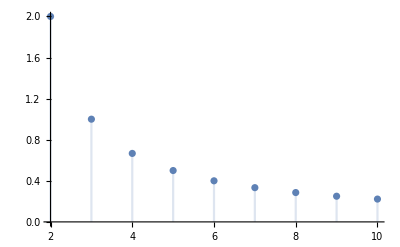

```mathematica
DiscretePlot[p[n],{n,2,10}]
```

nnnnnnnnnnnnnnnnnnnn

```mathematica
long=AssociationMap[ToString,Range@10];
RepeatedTiming@RandomChoice@long
long=AssociationMap[ToString,Range@1000000];
RepeatedTiming@RandomChoice@long
```

{1.24×10^-6,4}

{0.239,298738}

IMPORTANT!
GENERATING A LIST OF TEN TAKES AS MUCH TIME AS ONE
This might be true for Take as well and we could use te current scheme

This might help:
generate 100 (or 1000 or 10% of object size) choices and start going through and simulating one by one
at each step see if this site interacts with any of previous simulated if it doesnt then simulate, otherwise throw it out and move to next

```mathematica
long=AssociationMap[f,Range@1000000];
RepeatedTiming@RandomChoice[long,1]
RepeatedTiming@RandomChoice[long,10]
RepeatedTiming@RandomSample[long,1]
RepeatedTiming@RandomSample[long,10](*
RepeatedTiming@RandomSample[long,1000]*)
```

{0.281,{f[375865]}}

{0.279,{f[343949],f[891768],f[774090],f[658550],f[548296],f[181054],f[123925],f[297648],f[602066],f[264367]}}

{0.3898,<|141407→f[141407]|>}

{0.3897,<|408093→f[408093],932135→f[932135],466839→f[466839],330363→f[330363],324519→f[324519],327972→f[327972],137621→f[137621],49641→f[49641],950524→f[950524],389080→f[389080]|>}

I was thinking this email would be true, but now I am unsure

I don’t know how much you remember about the dewetting simulation I am working on, but there was only one operation that had bad scaling with the size of the system - selecting a random item from a very large association. I tried to avoid this by breaking my association into a Dataset, but the overhead of other operations on the dataset made it very slow for my purposes. Yesterday I found a solution.

create a huge association that describes everything in the solid
long = AssociationMap[f, Range@1000000];

We can pick a site at random in the following way; if we need to run 1000 times, this will cost me 1000*t0
t0 = Take[long, {RandomInteger[{1, Length @ long}]}];

However, picking many at once costs a fixed amount of time (t1=t2=t3=t4), where the t’s are
t1 = First @ RepeatedTiming @ RandomSample[long, 1];
t2 = First @ RepeatedTiming @ RandomSample[long, 10];
t3 = First @ RepeatedTiming @ RandomSample[long, 100];
t4 = First @ RepeatedTiming @ RandomSample[long, 1000];

t0 is less than t1, which is why I was using it
I just found out yesterday that 100 t0 > t3

So, if filtering the bulk random sample for non-interacting neighbors is faster than the time to just pick them at each run, then you can gain a benefit. This also prepares us to run each step in parallel.

```mathematica
long=Range@10;
RepeatedTiming@RandomChoice@long
long=ToString/@Range@1000000;
RepeatedTiming@RandomChoice@long
```

{6.16×10^-7,2}

{6.54×10^-7,216347}

```mathematica
ConstantArray[0,3]
```

{0,0,0}

```mathematica
Range@Length@short
```

{}

```mathematica
short=ConstantArray[0,10];
pos=RandomInteger[{1,Length@short}]
RepeatedTiming[short[[pos]]=1]
short

long=ConstantArray[0,1000000];
pos=RandomInteger[{1,Length@long}]
RepeatedTiming[long[[pos]]=1]
```

9

{6.45×10^-7,1}

{0,0,0,0,0,0,0,0,1,0}

873423

{6.9×10^-7,1}

```mathematica
short=ConstantArray[0,10];
RepeatedTiming[PrependTo[short,1]][[1]]
RepeatedTiming[AppendTo[short,1]][[1]]

long=ConstantArray[0,1000000];
RepeatedTiming[PrependTo[long,1]][[1]]
RepeatedTiming[AppendTo[long,1]][[1]]
```

4.9×10^-6

0.000019

0.00247

0.00248

```mathematica
{0.00001769888082015842433445708403727537`2.,}
```

{0.000018,Null}

Just keep the keys in a list and randomly choose from it!

```mathematica
Drop
```

Drop

#### definition

```mathematica
randomSurfaceSite[] := Block[
	{testAtomIndex},
	testAtomIndex = RandomInteger[{1, Length @ surfaceSites}];
	First @ Keys @ Take[surfaceSites, {testAtomIndex}]
]
```

```mathematica
Options[splitrKMC] = {"print all" -> False};

splitrKMC[testAtom_, temperature_, geometry_, OptionsPattern[]] := 
Block[
{
	testAtomIndex, neighborSites,
	occupiedNeighborSites, availableNeighborSites, totalPossibleMoves,
	candidateSite, rate, maxRate, pJump, jumpQ,
	newSite, occupiedNeighborsOfNewSite, mightHaveChanged,
	neighborsOfOccupiedNeighborsOfNewSite,
	nowInBulkQ, nowInBulk, nowOnSurface, neighborsOfNewSite,
	timingOfPick, timingOfP
},
If[Head@bad===Symbol,bad=0];
If[!KeyExistsQ[surfaceSites,testAtom],bad++;Return[];];
(*analyze neighborhood*)
neighborSites = neighbors[testAtom, geometry];
occupiedNeighborSites = Select[neighborSites, siteOccupiedQ];
availableNeighborSites = Complement[neighborSites, occupiedNeighborSites];
(*totalPossibleMoves = Length @ availableNeighborSites;*)
candidateSite = RandomChoice @ availableNeighborSites;

(*jump probability*)
pJump = AbsoluteTiming @ jumpProbability[temperature, testAtom, candidateSite, geometry];
timingOfP = pJump[[1]];
pJump = pJump[[2]];

jumpQ = RandomChoice[
	{pJump, 1 - pJump} -> {True, False}
];

If[
	jumpQ,

	newSite = candidateSite;

(*fact: old site is no longer in surfaceSites *)
	KeyDropFrom[surfaceSites, Key[testAtom]];
(*fact: newSite now on surface*)
	surfaceSites[newSite] = indexToCoordinate[newSite, geometry];

(*fact: if you were next to atom that left, then you are now on surface, you will alwats leave a vacancy*)
	
	occupiedNeighborSites = Select[occupiedNeighborSites, #[[3]] > 0 &];
	KeyDropFrom[surfaceSites, Key /@ occupiedNeighborSites];
	KeyDropFrom[bulkSites, Key /@ occupiedNeighborSites];
	Set[
		surfaceSites[#],
		indexToCoordinate[#, geometry]
	]& /@ occupiedNeighborSites;

(*occupiedNeighborsOfNewSite might have changed*)
	neighborsOfNewSite = neighbors[newSite, geometry];
	Set[
		occupiedNeighborsOfNewSite, 
		Select[
			neighborsOfNewSite,
			And[siteOccupiedQ @ #, #[[3]] > 0]&
		]
	];
(*If[
	Length@occupiedNeighborsOfNewSite==0,
	Print[
		Select[
			neighborsOfNewSite,
			siteOccupiedQ
		]
	];
];*)

	KeyDropFrom[surfaceSites, Key /@ occupiedNeighborsOfNewSite];
	KeyDropFrom[bulkSites, Key /@ occupiedNeighborsOfNewSite];

(*need to figure out what to do with occupiedNeighborsOfNewSite*)
	nowInBulk = Select[
		occupiedNeighborsOfNewSite, 
		(*all those that are completely surrounded*)
		With[
			{ns = neighbors[#,"FCC"]},
			And @@ (
					Or[
						KeyExistsQ[surfaceSites, #],
						KeyExistsQ[bulkSites, #],
						MemberQ[occupiedNeighborsOfNewSite, #],
						#[[3]] < 1
					]& /@ ns
			)
		]&
	];
	nowOnSurface = Complement[occupiedNeighborsOfNewSite, nowInBulk];
	
	Set[
		bulkSites[#],
		indexToCoordinate[#, geometry]
	]& /@ nowInBulk;
	Set[
		surfaceSites[#],
		indexToCoordinate[#, geometry]
	]& /@ nowOnSurface;
];

If[
	TrueQ @ OptionValue["print all"],
	Grid[{
		{
			viewSolid[
				surfaceSites, 
				bulkSites, 
				"FCC", 
				"start" -> indexToCoordinate[testAtom, "FCC"],
				"end" -> indexToCoordinate[candidateSite, "FCC"],
				"ImageSize" -> Full
			], 
			"initial site", testAtom
		},
		{SpanFromAbove, "possible moves", Length @ availableNeighborSites},
		{SpanFromAbove, "candidate site", candidateSite},
		{SpanFromAbove, "time of pick", timingOfPick},
		{SpanFromAbove, "probability", pJump},
		{SpanFromAbove, "time of p", timingOfP},
		{SpanFromAbove, "take jump?", jumpQ},
		{SpanFromAbove, "candidate site", candidateSite},
		{SpanFromAbove, Column[{"neighbors before", {"any", "substrate"}}], {Length @ Select[DeleteCases[neighbors[testAtom, geometry], candidateSite], siteOccupiedQ], Length @ Select[DeleteCases[neighbors[testAtom, geometry], candidateSite], #[[3]]<1&]}},
		{SpanFromAbove, Column[{"neighbors after", {"any", "substrate"}}], {Length @ Select[DeleteCases[neighbors[candidateSite, geometry], testAtom], siteOccupiedQ], Length @ Select[DeleteCases[neighbors[candidateSite, geometry], testAtom], #[[3]]<1&]}}
	}, Alignment->{Left,Top}, Spacings->{3, 1},ItemSize->{{Scaled[.6], Scaled[.2],Scaled[.2]}}]
]

]
```

#### SHARE - step-by-step usage

at around 20x20x20 = 32000 atoms the time required to select the random atom and the time required to calculate it’s jump rate are equivalent ~10^-4. The jump rate has no scaling issues, but the random site selection does. We need some way to partition the problem.

I have used RandomSample to partition it since somehow it can get 100 random sites for the price of 1 and the chance of grabbing sites that would interact is very low

laptop testing

old 9k atoms 1k steps 0.75 secs 

new 9k atoms 1k steps
time | sample size | repeats
1.36 | 200 | 5
.52 | 125 | 8
.465 | 100 | 10
.59 | 50 | 20

old 9k atoms 10k steps 13.8 secs 

new 9k atoms 10k steps
time | sample size | repeats
7.3 | 2000 | 5
7.38 | 1000 | 10
7.46 | 500 | 20
7.45 | 200 | 50
6.9 | 100 | 100
9.0 | 50 | 200
7.5 | 20 | 500
20 | 2 | 5000

old 9k atoms 50k steps 65.3 secs 

new 5k atoms 50k steps
time | sample size | repeats
33.6 | 1000 | 50
34.76 | 500 | 100
37.2 | 100 | 500
36 | 50 | 1000

old 10k atoms 50k steps is ~90.9 secs
new 10k atoms 50k steps is ~40.4 secs

old 20k atoms 50k steps is ~131.2 secs
new 20k atoms 50k steps is ~38.4 secs

That means:
46% improvement for 5k atoms
55% improvement for 10k atoms
69% improvement for 20k atoms

And most importantly there seems to be no more scaling issue for the simulation, it is now a fix time per iteration no matter how big the solid is!!!

Hooray! Using RandomSample provides better scaling!!!

```mathematica
surfaceSites=<||>;
bulkSites=<||>;
solidSites=<||>;
bad=0;

angle=RandomReal[{0,Pi}];
temp=5;
createWire[5,5,100,0,angle];
findSurface["FCC"]
Length@surfaceSites+Length@bulkSites

step=0;
Monitor[
First@AbsoluteTiming@Do[
step++;
sites=Keys@RandomSample[surfaceSites,500];
(*need to filter sites, right now this causes collisions*)
(*either divide up front or as you map check for things that were successful and append those to a list*)
splitrKMC[#,temp, "FCC", "print all"->False]&/@sites;
,
1000
],step
]

(*viewSolid[surfaceSites,bulkSites,"FCC"]*)
```

8999

152.991

```mathematica
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

```mathematica
step=0;
Monitor[
First@AbsoluteTiming@Do[
step++;
sites=Keys@RandomSample[surfaceSites,500];
(*need to filter sites, right now this causes collisions*)
(*either divide up front or as you map check for things that were successful and append those to a list*)
splitrKMC[#,temp, "FCC", "print all"->False]&/@sites;
,
1000000
],step
]
```

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
viewSolid[surfaceSites,bulkSites,"FCC"]
```

-Graphics3D-

some time passed
-Graphics3D-

some more time passed
-Graphics3D-

more
-Graphics3D-

more
-Graphics3D-

a lot more 
-Graphics3D-

-Graphics3D-

5.3 seconds for 100x100 steps

NEW ( grab this many in the list “x” do it this many times )
38k atoms
1x1000		1.6
10x100 	0.4
100x10 	0.3
200x05		0.5
1000x1 	0.6

OLD
38k atoms
1000 steps	0.589543 seconds

70k atoms	
1000 steps	0.894661

OLD
3502 | 100k | 48.8438
  | 1M | 512.578

```mathematica
5/10000//N
```

0.0005

#### SHARE - real simulation usage

```mathematica
createSolid[2,2,2,"FCC"];
findSurface["FCC"];
Length@surfaceSites+Length@bulkSites
viewSolid[surfaceSites,bulkSites,"FCC"]
AbsoluteTiming[Do[rKMC[10, "FCC"],1000]]
viewSolid[surfaceSites,bulkSites,"FCC"]
Length@surfaceSites+Length@bulkSites
```

32

-Graphics3D-

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of RandomChoice[{}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification FCC⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

{0.970404,Null}

-Graphics3D-

971